### A Bayesian take on the Schrodinger equation

The Schrodinger equation is a model for how the wave function of a quantum system evolves over time. It takes many forms in many contexts, and is notoriously opaque to students who are first being introduced to quantum theory. Here I will offer an explanation that relies primarily on Bayesian statistics.


We’ll start with a very simple physical model for a free particle in one dimension with no forces acting upon it. We’ll let x(t) be the particle’s position at time t.  Newton’s laws tell us that without any forces acting on the particle it will move along with a constant velocity forever. In differential equation terms we can say that x'(t)=v where v is the initial velocity of the particle. Solving this very simple differential equation gives us a closed form trajectory for the particle, given by x(t)=x(0)+v t. 

This means that we can entirely parametrize the particle’s trajectory with two variables: x(0) and v.

Suppose that now we are uncertain about the particles initial position and velocity, but we have some distribution for them. Suppose that the initial position and velocity are each independent, and that we have some prior normal distribution for them. By creating an ensemble of particles we can simulate how our distribution should evolve over time. Let’s call the initial mean and variance of position μ_xand σ_x, and the mean and variance of the velocity μ_vand σ_v.

Let’s create a function which generates trajectories given initial conditions.

```mathematica
x[x0_,v_][t_]:=x0+v t
```

And then we can generate an ensemble of particles to simulate how the distribution will change over time.

```mathematica
(*Make some distrubutions for x(0) and v*)
x0Dist[μx_,σx_]:=NormalDistribution[μx,σx];
vDist[μv_,σv_]:=NormalDistribution[μv,σv];
(*Some parameters for the distributions*)
μx=0;
σx=1;
μv=2;
σv=1;

(*generate the ensamble of tradjectories*)
ensamble=Array[
x[
RandomVariate[x0Dist[μx,σx]],
RandomVariate[vDist[μv,σv]]
]&
,10000];
(*function to evaluate the ensamble at time t*)
ensambleAt[t_]:=#[t]&/@ensamble

(*controls for the ensamble*)
ensControls=Manipulate[
{μx,σx,μv,σv}={μxl,σxl,μvl,σvl};
ensamble=Array[x[RandomVariate[x0Dist[μx,σx]],RandomVariate[vDist[μv,σv]]]&,5000];
{{"μ_x",μx},{"σ_x",σx},{"μ_v",μv},{"σ_v",σv}}//TableForm,
{{μxl,0,"μ_x"},-10,10},
{{σxl,1,"σ_x"},.1,5},
{{μvl,2,"μ_v"},-10,10},
{{σvl,1,"σ_v"},.1,5},
BaselinePosition->Top
];
(*controls for the simulation*)
simControls=Manipulate[
Dynamic[Histogram[
ensambleAt[t],{.5},"PDF",
PlotRange->{{-10,10},{0,1}},
AxesOrigin->{0,0},
AxesLabel->{"x","PDF"},
ImageSize->Large
]],
{t,0,10},
BaselinePosition->Top
];
Row[{ensControls,simControls}]
```

If you don’t have access to the manipulate for whatever reason, here are some time slices:

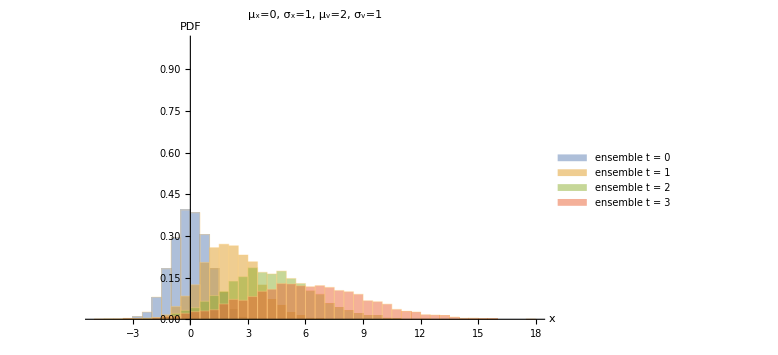

```mathematica
(*some styling that will make a future graphic better*)
colors=ColorData[97,"ColorList"];

ensambleSlices=Histogram[
Table[
ensambleAt[t],{t,{0,1,2,3}}
]//Evaluate,
{.5},"PDF",
PlotRange->{All,{0,1}},
AxesOrigin->{0,0},
AxesLabel->{"x","PDF"},
ImageSize->Large,
ChartLegends->Table["ensemble t = "<>ToString@t,{t,{0,1,2,3}}],
PlotLabel->"μ_x="<>ToString@μx<>", σ_x="<>ToString@σx<>", μ_v="<>ToString@μv<>", σ_v="<>ToString@σv,
ChartStyle->colors
]
```

This result makes a lot of sense. Overall the mean position is moving to the right, since the mean velocity is greater than zero. However, since there is some variance in the velocity, the distribution spreads out over time.

Numerical simulation is great for verification, but it is also somewhat slow and difficult to analyze rigorously. To generate an analytical solution, we need only think of the evolution of time as a continuous sequence of Bayesian updates.

To do this, we will have to account for all of our state variables. Even though velocity is constant in this example, it is not perfectly known, and must be thought of as a state variable. This means that we are looking for P(x,v|t), the probability of being at position x moving at velocity v at time t. The likelihoods are easy to calculate, since we can just run the simulation back to t=0 and sample the initial distribution. Let’s call ϕ(x,v) the initial distribution.

```mathematica
ϕ[μx_,σx_,μv_,σv_][x_,v_]:=PDF[x0Dist[μx,σx]][x]PDF[vDist[μv,σv]][v]
Like[μx_,σx_,μv_,σv_][xl_,v_,t_]:=ϕ[μx,σx,μv,σv][x[xl,v][-t],v]
Manipulate[
ContourPlot[
Quiet[Like[μx,σx,μv,σv][xl,v,t]],{xl,-10,10},{v,-10,10},
PlotRange->All,
PlotPoints->ControlActive[30,50],
MaxRecursion->ControlActive[0,1],
FrameLabel-> {x,v},
PlotLegends->Automatic,
PlotLabel->"Likelihoods at t="<>ToString@t
],
{{μx,0,"μ_x"},-10,10},
{{σx,1,"σ_x"},.1,5},
{{μv,2,"μ_v"},-10,10},
{{σv,1,"σ_v"},.1,5},
{t,0,3}
]
```

And of course, for those without Mathematica, we present some time slices:

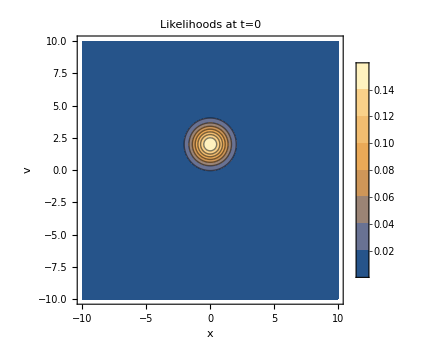
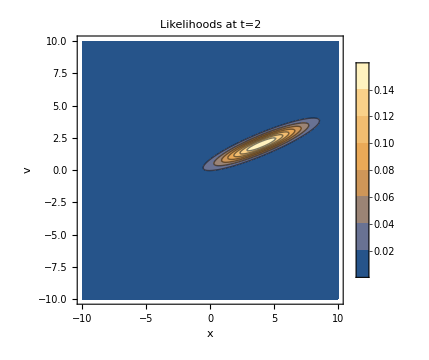
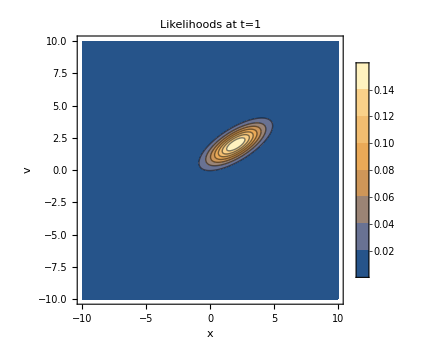
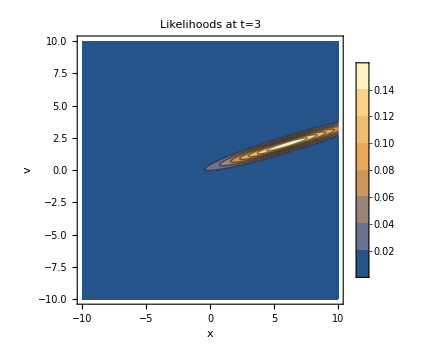
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Multicolumn@Table[
ContourPlot[
Quiet[Like[μx,σx,μv,σv][xl,v,t]],{xl,-10,10},{v,-10,10},
PlotRange->All,
FrameLabel-> {x,v},
PlotLegends->Automatic,
PlotPoints->50,
MaxRecursion->3,
PlotLabel->"Likelihoods at t="<>ToString@t,
ImageSize->Medium
],
{t,{0,1,2,3}}]
```

Again, this makes sense. The fast parts move right faster, and the slow parts move right slower. Generally it looks like our distribution gets sheared along the diagonal.

We can then get the posterior probabilities by normalizing the data:

```mathematica
cacheVars:=cache={μx,σx,μv,σv};ClearAll[μx,σx,μv,σv];$Assumptions={xl∈Reals,v∈Reals,t>0,μx∈Reals,σx>0,μv∈Reals,σv>0};
uncacheVars:={μx,σx,μv,σv}=cache;
cacheVars;
Integrate[Like[μx,σx,μv,σv][xl,v,t],{xl,-∞,∞},{v,-∞,∞}]//Simplify
uncacheVars;
```

1

And wouldn’t you know, our system is inherently probability conserving! Isn’t that sweet. This means that our posterior probabilities are our likelihoods! Actually, we could have guessed this by looking at how the likelihoods evolve over time. Since shearing is area-conservative, it makes sense that the total likelihood is always equal to the original.

```mathematica
cacheVars;
Like[μx,σx,μv,σv][x,v,t]
uncacheVars;
```

(ⅇ^(-1/2 (-2+v)^2-1/2 (-t v+x)^2))/(2 π)

So P(x,v|t)=(ⅇ^(-(v-μv)^2/(2 σv^2)-(-t v+x-μx)^2/(2 σx^2)))/(2 π σv σx).

And now, to get back to the pretty graphs from before, we can integrate out v to get the x marginal for the posterior.

```mathematica
cacheVars;
Integrate[Like[μx,σx,μv,σv][x,v,t],{v,-∞,∞}]//Simplify
uncacheVars;
```

(ⅇ^(-(-x+t μv+μx)^2/(2 (t^2 σv^2+σx^2))))/(√(2 π) √(t^2 σv^2+σx^2))

So P(x|t)=(ⅇ^(-(-x+t μv+μx)^2/(2 (t^2 σv^2+σx^2))))/(√(2 π) √(t^2 σv^2+σx^2)). With this result, we can make some more pretty animations and graphs of the probability distribution over time.

```mathematica
P[μx_,σx_,μv_,σv_][x_,t_]:=(ⅇ^(-(-x+t μv+μx)^2/(2 (t^2 σv^2+σx^2))))/(√(2 π) √(t^2 σv^2+σx^2))
Manipulate[
Plot[P[μx,σx,μv,σv][xl,t],{xl,-10,10},
PlotRange->{All,{0,1}},
Filling->Axis,AxesOrigin->{0,0},
AxesLabel->{"x","PDF"},
ImageSize->Large
],
{{μx,0,"μ_x"},-10,10},
{{σx,1,"σ_x"},.1,5},
{{μv,2,"μ_v"},-10,10},
{{σv,1,"σ_v"},.1,5},
{t,0,3}
]
```

And, once more for those who cannot drag the fancy sliders around, we present some time slices:

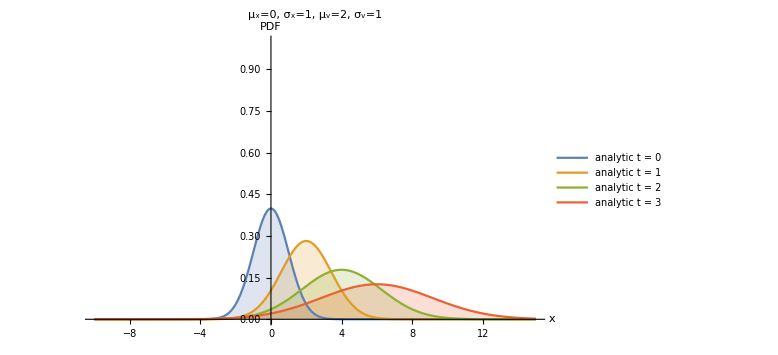

```mathematica
analyticSlices=Plot[Table[P[μx,σx,μv,σv][xl,t],{t,{0,1,2,3}}]//Evaluate,{xl,-10,15},
PlotRange->{All,{0,1}},
Filling->Axis,AxesOrigin->{0,0},
AxesLabel->{"x","PDF"},
ImageSize->Large,
PlotLegends->Table["analytic t = "<>ToString@t,{t,{0,1,2,3}}],
PlotLabel->"μ_x="<>ToString@μx<>", σ_x="<>ToString@σx<>", μ_v="<>ToString@μv<>", σ_v="<>ToString@σv
]
```

And for verification, we can look at both the analytic and ensemble models together:

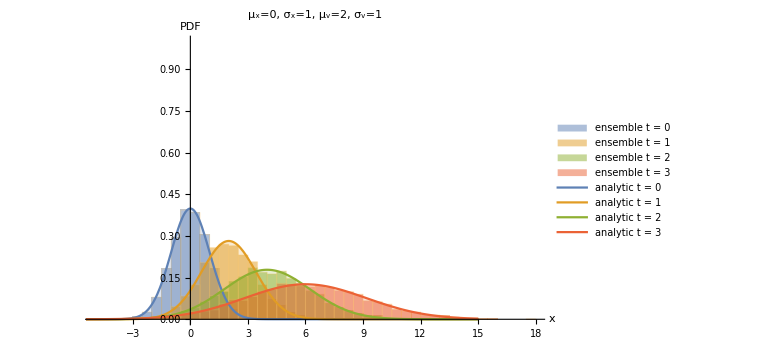

```mathematica
Show@{ensambleSlices,analyticSlices}
```

So yes, our analytic solution is correct!

We can even make a nice manipulate for the verification, to really drive the point home:

```mathematica
(*controls for the varification*)
varControls=Manipulate[
Dynamic[
Show@{
Plot[P[μx,σx,μv,σv][xl,t],{xl,-12,12},
PlotRange->{{-10,10},{0,1}},
Filling->Axis,AxesOrigin->{0,0},
AxesLabel->{"x","PDF"},
ImageSize->Large
],
Histogram[
ensambleAt[t],{.5},"PDF",
PlotRange->{{-10,10},{0,1}},
AxesOrigin->{0,0},
AxesLabel->{"x","PDF"},
ImageSize->Large,
ChartStyle->Directive[colors[[1]],Opacity[.1]]
]
}
],
{t,0,4},
BaselinePosition->Top
];
Row[{ensControls,varControls}]
```

### That other model

To really show that this is working, we should demonstrate that it qualitatively matches the behaviour of the original flavor Schrodinger equation. Since this is a draft, I’m just going to link another Mathematica demonstration that they do in fact match up. This was copied from the wolfram demonstrations project. Specifically, it is a modified version of this demonstration:

Andrés Santos “Wavepacket for a Free Particle”
http://demonstrations.wolfram.com/WavepacketForAFreeParticle/
Wolfram Demonstrations Project
Published: January 15 2009 

Which I adapted to fit the overall format of this presentation.

```mathematica
a[Δp_,t_]:=1/(4(Δp)^2)+I t/2;
 
b[p0_,Δp_,x_]:=p0/(2(Δp)^2)+I x;
 
c[p0_,Δp_]:=-p0^2/(4(Δp)^2) (*Auxiliary quantities*)
```

```mathematica
Ψ[p0_,Δp_,x_,t_]:=(2π (Δp)^2 4a[Δp,t]^2)^(-1/4)E^(c[p0,Δp]+b[p0,Δp,x]^2/(4a[Δp,t])) (*Wave packet corresponding to an initial Gaussian wavefunction*)
```

```mathematica
Prob[p0_,Δp_,x_,t_]:=Ψ[p0,Δp,x,t]Conjugate[Ψ[p0,Δp,x,t]] (*Probability density*)
```

```mathematica
F[p0_,Δp_,x_,t_,j_]:={Re[Ψ[p0,Δp,x,t]],Im[Ψ[p0,Δp,x,t]],Prob[p0,Δp,x,t]}[[j]](*Choice of function to be plotted*)
```

```mathematica
k[p0_,Δp_,n_]:=p0+(n-3)Δp (*Characteristic momenta*)
```

```mathematica
ReΨ[p0_,Δp_,x_,t_,n_]:=1/(√(2π))(2π(Δp)^2)^(-1/4)E^(-(k[p0,Δp,n]-p0)^2/(2 Δp)^2)Cos[k[p0,Δp,n]x-k[p0,Δp,n]^2/2 t]+(n-3) 2 1/(√(2π))(2π(Δp)^2)^(-1/4) (*Real part of the characteristic harmonic waves (raised for easier visibility)*)
```

```mathematica
Fmin[Δp_,j_]:={-(2π/(2 Δp)^2)^(-1/4),-(2π/(2 Δp)^2)^(-1/4),-(2π/(2 Δp)^2)^(-1/2)/50}[[j]](*Lower limit of the vertical axis*)
```

```mathematica
Fmax[Δp_,j_]:={(2π/(2 Δp)^2)^(-1/4),(2π/(2 Δp)^2)^(-1/4),(2π/(2 Δp)^2)^(-1/2)}[[j]](*Upper limit of the vertical axis*)
```

```mathematica
tmax=50;
```

```mathematica
Manipulate[
Plot[Table[F[p0,Δp,x,t,3],{t,0,50,10}]//Evaluate,{x,-Max[4/Δp,p0  tmax],Max[4/Δp,p0  tmax]},PlotRange->{Fmin[Δp,3],Fmax[Δp,3]},ImageSize->{500,350},Filling->Axis,PlotLegends->Table["t="<>ToString@t,{t,0,50,10}]], {{p0,1,"average momentum, <p>"},0,1,Appearance->"Labeled"},{{Δp,.25,"momentum uncertainty, Δp"},.1,1,Appearance->"Labeled"}, SaveDefinitions->True]
```

Assuming that Andrés Santos got it right, it looks like the Schrodinger equation predicts the same behavior for free particles as this Bayesian model. Nice!